## Stability diagram plot

### Stability diagram plot

```mathematica
ClearAll["Global`*"];
```

#### Defenitions

```mathematica
Eq1=-Sqrt[(Qm/Qp)] (Sqrt[1-a^2] γa+a γp)+κ (-1+((2 Qm γ+γd) μ)/(γd+Qp (γ+γd)+Qm (γ+4 Qp γ+γd)));
Eq2=Sqrt[Qp/Qm] (-Sqrt[1-a^2] γa+a γp)+κ (-1+((2 Qp γ+γd) μ)/(γd+Qp (γ+γd)+Qm (γ+4 Qp γ+γd)));

Eq3=a (Sqrt[Qm/Qp]+Sqrt[Qp/Qm]) γa+(-Sqrt[((Qm-a^2 Qm)/Qp)]+Sqrt[(Qp-a^2 Qp)/Qm]) γp+(2 (Qm-Qp) α γ κ μ)/((Qm+Qp+4 Qm Qp) γ+(1+Qm+Qp) γd);

Ns=((Qm γ+Qp γ+γd) μ)/(Qm γ+Qp γ+4 Qm Qp γ+γd+Qm γd+Qp γd);

ns=((Qm-Qp) γ μ)/(Qm γ+Qp γ+4 Qm Qp γ+γd+Qm γd+Qp γd);

ω=Sqrt[Qp/Qm] ((α γa-γp) Cos[2 ψ]-(γa+α γp) Sin[2 ψ]);

M={{-Sqrt[(Qm/Qp)] (-Sqrt[1-a^2] γa-a γp),-Sqrt[(Qm/Qp)] (-a γa+Sqrt[1-a^2] γp),-Sqrt[1-a^2] γa-a γp,-a γa+Sqrt[1-a^2] γp,Sqrt[Qp] κ,Sqrt[Qp] κ},{Sqrt[Qm/Qp] (-a γa+Sqrt[1-a^2] γp),-Sqrt[(Qm/Qp)] (-Sqrt[1-a^2] γa-a γp),a γa-Sqrt[1-a^2] γp,-Sqrt[1-a^2] γa-a γp,Sqrt[Qp] α κ,Sqrt[Qp] α κ},{-Sqrt[1-a^2] γa+a γp,a γa+Sqrt[1-a^2] γp,-Sqrt[(Qp/Qm)] (-Sqrt[1-a^2] γa+a γp),Sqrt[Qp/Qm] (-a γa-Sqrt[1-a^2] γp),Sqrt[Qm] κ,-Sqrt[Qm] κ},{-a γa-Sqrt[1-a^2] γp,-Sqrt[1-a^2] γa+a γp,-Sqrt[(Qp/Qm)] (-a γa-Sqrt[1-a^2] γp),-Sqrt[(Qp/Qm)] (-Sqrt[1-a^2] γa+a γp),Sqrt[Qm] α κ,-Sqrt[Qm] α κ},{-2 ns Sqrt[Qp] γ-2 Ns Sqrt[Qp] γ,0,2 ns Sqrt[Qm] γ-2 Ns Sqrt[Qm] γ,0,-γ-Qm γ-Qp γ,Qm γ-Qp γ},{-2 ns Sqrt[Qp] γ-2 Ns Sqrt[Qp] γ,0,-2 ns Sqrt[Qm] γ+2 Ns Sqrt[Qm] γ,0,Qm γ-Qp γ,-Qm γ-Qp γ-γd}};
```

#### Solution

```mathematica
(*Solving stationary problem*)
γa=-0.01;
γ=1.;
γp=10;
κ=300.;
γd=50.;
α=3.;
μ=1.7;
Qp0=0.9;
Qm0=0.1;
a0=-0.1;

Nsol=FindRoot[{Eq1==0,Eq2==0,Eq3==0},{{Qp,Qp0,N[10^-8],10.},{Qm,Qm0,N[10^-8],10.},{a,a0,-1.,1.}}]

(*Evaluating charpoly*)

p=CoefficientList[CharacteristicPolynomial[M/.Nsol,λ],λ];
If[AllTrue[p,Positive],
DH=ConstantArray[0,5];
DH[[1]]=p[[6]];
DH[[2]]=p[[6]]*p[[5]]-p[[7]]*p[[4]];
DH[[3]]=p[[4]]*DH[[2]]-p[[6]]*p[[6]]*p[[3]]+p[[2]]*p[[7]]*p[[6]];
DH[[4]]=p[[3]]*DH[[3]]+p[[7]]*p[[2]]*(p[[5]]*p[[4]]-p[[7]]*p[[2]])-p[[6]]*(p[[5]]*p[[5]]*p[[2]]-p[[7]]*p[[3]]*p[[2]]-p[[1]]*DH[[2]]);
DH[[5]]=p[[2]]*DH[[4]]+p[[1]]*(p[[7]]*p[[4]]*p[[4]]*p[[4]]-p[[6]]*p[[4]]*(p[[5]]*p[[4]]+2*p[[7]]*p[[2]])+p[[6]]*p[[6]]*(p[[4]]*p[[3]]+p[[5]]*p[[2]])-p[[6]]*p[[6]]*p[[6]]*p[[1]]);
If[AllTrue[DH,Positive],
Print["System is stable"];
Print[p//MatrixForm];
Print[DH//MatrixForm],
Print["Some Hurwitz determinants are negative:"];
Print[p//MatrixForm];
Print[DH//MatrixForm]
],
Print["Some p < 0"];
Print[p//MatrixForm]
]
```

{Qp→0.560309,Qm→0.134562,a→-0.200743}

Some Hurwitz determinants are negative:

(5.97979×10^-9
4.78818×10^6
416569.
29191.3
1220.32
46.2142
1)

(46.2142
27205.
1.25741×10^8
-3.73298×10^13
-1.78742×10^20)

```mathematica
Nμ=100;
Nγp=100;
μs=CoordinateBoundsArray[{{1.,6.}},Into[Nμ]]//Flatten;
γps=CoordinateBoundsArray[{{1.,2.}},Into[Nγp]]//Flatten//Power[10,#]&;
result=ConstantArray[0,{Nγp,Nμ}];
For[i=1,i<= Nμ,i++,
For[j=1,j<= Nγp,j++,
μ=μs[[i]];
γp=γps[[j]];
Nsol=FindRoot[{Eq1==0,Eq2==0,Eq3==0},{{Qp,Qp0,N[10^-8],10.},{Qm,Qm0,N[10^-8],10.},{a,a0,-1.,1.}}];
p=CoefficientList[CharacteristicPolynomial[M/.Nsol,λ],λ];
p[[1]]=0;

If[AllTrue[p,NonNegative],
DH=ConstantArray[0,5];
DH[[1]]=p[[6]];
DH[[2]]=p[[6]]*p[[5]]-p[[7]]*p[[4]];
DH[[3]]=p[[4]]*DH[[2]]-p[[6]]*p[[6]]*p[[3]]+p[[2]]*p[[7]]*p[[6]];DH[[4]]=p[[3]]*DH[[3]]+p[[7]]*p[[2]]*(p[[5]]*p[[4]]-p[[7]]*p[[2]])-p[[6]]*(p[[5]]*p[[5]]*p[[2]]-p[[7]]*p[[3]]*p[[2]]-p[[1]]*DH[[2]]);DH[[5]]=p[[2]]*DH[[4]]+p[[1]]*(p[[7]]*p[[4]]*p[[4]]*p[[4]]-p[[6]]*p[[4]]*(p[[5]]*p[[4]]+2*p[[7]]*p[[2]])+p[[6]]*p[[6]]*(p[[4]]*p[[3]]+p[[5]]*p[[2]])-p[[6]]*p[[6]]*p[[6]]*p[[1]]);

If[AllTrue[DH,Positive],
If[Abs[Qp-Qm/.Nsol]<10^-8,result[[i,j]]=1,result[[i,j]]=0.7],
result[[i,j]]=0.5;
],
result[[i,j]]=0;
]
]
];
Image[Reverse[result]]
```

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindRoot::lstol will be suppressed during this calculation.

FindRoot::reged: The point {0.107997,0.906551,1.} is at the edge of the search region {1.×10^-8,10.} in coordinate 1 and the computed search direction points outside the region.

FindRoot::reged: The point {0.123634,0.910422,1.} is at the edge of the search region {1.×10^-8,10.} in coordinate 1 and the computed search direction points outside the region.

FindRoot::reged: The point {0.139076,0.914214,1.} is at the edge of the search region {1.×10^-8,10.} in coordinate 1 and the computed search direction points outside the region.

General::stop: Further output of FindRoot::reged will be suppressed during this calculation.

-Graphics-

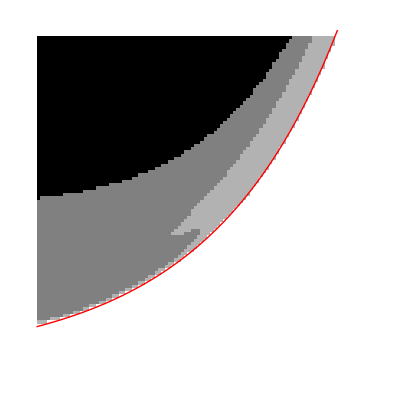

```mathematica
ap=ArrayPlot[1-Reverse[result]];
Mu[γp_]:=(κ+γa)*(α *γ *κ+α *γ *γa-γ *γp+γp *γd)/(γ *κ *(α *κ+α *γa-γp));

lp=Plot[(Mu[10*10^(x/Nγp)]-1)/5*Nμ,{x,0,Nγp},PlotStyle-> {Red,Thick}];
Show[ap,lp,PlotRange-> {{0,Nγp},{0,Nμ}}]
```